```mathematica
(* constants*)
(*https://en.wikipedia.org/wiki/Avogadro_constant*)
N0=6.02214076*10^23;
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
me=9.10938291*10^(-28);
mev=0.510998928;
(*Positron lifetime*)
tpo=0.4787*10^(-9);
(*Bohr radius*)
rb=5.29*10^(−9);
(*single monopole charge*)
Qm=2*Pi*hbar/e;
(*http://en.wikipedia.org/wiki/Fine-structure_constant*)
Clear[Ql]
Ql=Table[Ql/.Solve[ml[[i]]==(8*Pi/3)*Ql^3,Ql][[3]],{i,3}]
α=1/137.035999206;
αw=0.42541281596347497;
(*From:https://en.wikipedia.org/wiki/Fermi%27s_interaction*)
Gf=1.4327038609285911*^-49;
Ω=0.0078749969978123844;
kb=1.380658*10^(-16);
omega=0.00787499699;
(*calculated already unified*)
mH=126.22136632802759*10^3*me/mev;
mp=1.672621777*10^(-24);
mn=1838.6402*me;
(*http://en.wikipedia.org/wiki/Weinberg_angle*)
θw0=0.231208;
θwrad=ArcSin[Sqrt[0.231208]];
θwdeg=θwrad*180/Pi;
(*https://en.wikipedia.org/wiki/Precision_tests_of_QED*)
g=2*1.00115965218085;
(* unification mass:anti-deSitter model*)
muni=3.6543166832631125*^-12;
mtau=1776.82*me/mev;
mmu=105.6583715*me/mev;
mpi=139.57018*me/mev;
mhiggs=125.38*10^3*me/mev;
mz=91.1876*10^3*me/mev;
mw=80.4335*10^3*me/mev;
mtop=172.93*10^3*me/mev;
mbottom=4.1*10^3*me/mev;
mcharm=1.275*10^3*me/mev;
mstrange=92.4*me/mev;
momegassb=6054.4/10^3;
mplanck=Sqrt[hbar*c/G];
mup=2.01*me/mev;
md0=4.79*me/mev;
(* log linear fit for 4th level quarks*)
mwhite=1.1677931388727855*^-19;
mblack=1.8611487827001873*^-22;
mout=1.5020666505936996*^-20;
Tvac=2.72548;
(*http://en.wikipedia.org/wiki/Observable_universe*)
ru=8.8*10^28/2;
rplanck=2*Pi*hbar/(mplanck*c);
tplanck=rplanck/c;
(*http://en.wikipedia.org/wiki/Big_Bang*)
(*years*days*hours*minutes*seconds*)
tu=13.798*10^9*365.25*24*60*60;
mnu=1.78266270 * 10^(-33 );
mnumu=6.7978246932973695*^-31;
mnutau=1.1431743145263108*^-29;
```

{4.77299×10^-10,2.8224×10^-9,7.23099×10^-9}

```mathematica
(*New universe age: Some Old Globular Clusters (and Stars) Inferring That the
Universe Is Older Than Commonly Accepted
Félix Llorente de Andrés*)
tun=26.7*10^9*365.25*24*60*60;
run=c*tun;
```

```mathematica
(*Weak charge on 5d simplex*)
Cw=(3!*2!)*Det[{{α,0,0,0,0,1},{0,α,0,0,0,1},{0,0,α,0,0,1},{0,0,0,α,0,1},{0,0,0,0,α,1},{0,0,0,0,0,1}}]/5!;
rw=Cw^2/(mnu*c^2);
(*http://www.bottomlayer.com/bottom/deutsch/neutrino.html*)
(* Weeks volume*)
vw=0.94270736277692772092;

(* Thurston-Meyerhoff volume*)
vt=0.981368828892232088914;
(*lepton hyperbolic 3 manifold volume*)
vl=(18/24)*vt;
pizero=134.9766*me/mev;
(* Bohr radius: https://en.wikipedia.org/wiki/Bohr_radius*)
ab=5.2917721067*10^(-9);
(*:https://en.wikipedia.org/wiki/Pion:*)
tpip=2.6033*10^(−8 );
tpiz=8.4*10^(−17);
(* product quarks masses in me*)
mup1=12.239779918021176;mdp1=12.256361761325056;
(* elliptic product quarks for Pi mesons*)
mupi=16.25229214603282;mdpi=16.805755043381577;
mqmu=Sqrt[mmu/me];
mqtau=Sqrt[mtau/me];
(* hadron strange and charm product quark masses*)
mqs=mqtau*mup1/mqmu;
mqc=2*mqs;
ttau=2.932*10^(−13);
tmu=2.1969811*10^(−6);
(*.10https://physicstoday.scitation.org/doi/10.1063/PT.3.4424*)
(*.10https://physics.stackexchange.com/questions/134856/units-of-hubble-time-and-hubble-constant*)
Hcbm=67.4/(3.09*10^19);
Hsnova=74.0/(3.09*10^19);
Hlense=73.3/(3.09*10^19);
Have=73.8/(3.09*10^19);
H0=2.2894835758225842*^-18;
th0=1/H0;
(* CMB age*)
tcmb=372000*365.25*24*60*60;
tsnova=1/Hsnova;
msun=1.9891*10^33;
(*first approximation electron g:single loop GED:weak g'*)
g0=2*(1+α/2);
Clear[g1]
g1=g1/.Solve[(g1/Sqrt[g+g1^2])^2==0.231208,g1][[2]];
(* gravity momemt γ*)
γ=e*G/(hbar*c);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*elliptical Lepton*)
```

```mathematica
ml={me,mmu,mtau}
```

{9.10938×10^-28,1.88353×10^-25,3.16747×10^-24}

```mathematica
Clear[Ql]
```

```mathematica
Ql=Table[Ql/.Solve[ml[[i]]==(8*Pi/3)*Ql^3,Ql][[3]],{i,3}]
```

{4.77299×10^-10,2.8224×10^-9,7.23099×10^-9}

```mathematica
(*Hperbolic Bosons*)
mb={mw,mz,mhiggs}
```

{1.43386×10^-22,1.62557×10^-22,2.2351×10^-22}

```mathematica
Clear[Qb]
```

```mathematica
Qb=Table[Qb/.Solve[mb[[i]]==(3/4)*Qb^3,Qb][[3]],{i,3}]
```

{5.76078×10^-8,6.00686×10^-8,6.67952×10^-8}

```mathematica
Q=Join[Ql,Qb]
```

{4.77299×10^-10,2.8224×10^-9,7.23099×10^-9,5.76078×10^-8,6.00686×10^-8,6.67952×10^-8}

```mathematica
Q/e
```

{0.993708,5.87607,15.0545,119.936,125.059,139.064}

```mathematica
Apply[Plus,{0.9937081053629031,5.876067916342784,15.054510787953797,119.93619651059954,125.0594587976244,139.06378260736028}]/6
```

67.664

```mathematica
f[x_]=Fit[Q/e-67.66395412087394,Join[{1*(x-3.5)/(1+(x-3.5)^2)},Table[x^i,{i,0,5}]],x]
```

-63.6517+(144.737 (-3.5+x))/(1+(-3.5+x)^2)+59.2296 x-11.818 x^2-0.705012 x^3+0.173749 x^4+0.0105862 x^5

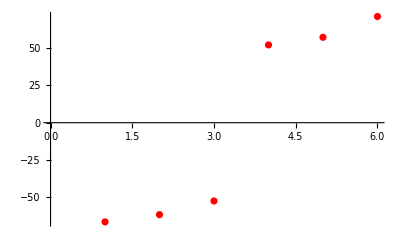

```mathematica
gq=ListPlot[Q/e-67.66395412087394,PlotStyle->Red]
```

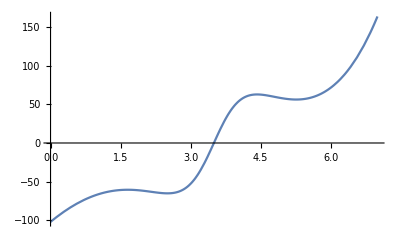

```mathematica
gf=Plot[f[x],{x,0,7}]
```

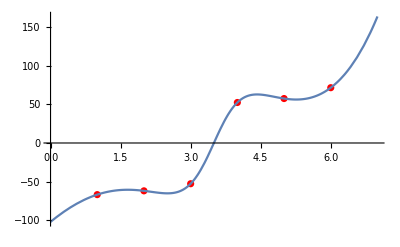

```mathematica
Show[{gq,gf},PlotRange->All]
```

```mathematica
mel=Table[(8*Pi/3)*((f[i]+67.66395412087394)*e)^3,{i,0,7,0.5}]/me
```

{-40838.8,-2150.08,1.,342.37,206.768,19.1779,3477.15,319747.,1.75822×10^6,2.24608×10^6,1.9933×10^6,1.99752×10^6,2.74073×10^6,5.22949×10^6,1.25688×10^7}

```mathematica
mhp=Table[(3/4)*((f[i]+67.66395412087394)*e)^3,{i,0,7,0.5}]/mhiggs
```

{-0.0149007,-0.000784494,3.64867×10^-7,0.000124919,0.0000754429,6.99739×10^-6,0.0012687,0.116665,0.641518,0.819522,0.72729,0.728827,1.,1.90807,4.58593}

```mathematica
sq=Table[s/.Solve[Q[[i]]==e/α^s,s][[1]],{i,Length[Q]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{-0.00128282,0.359919,0.551127,0.972911,0.981413,1.00299}

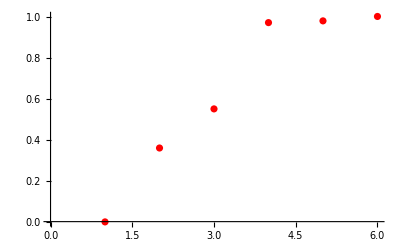

```mathematica
ga=ListPlot[sq,PlotStyle->Red]
```

```mathematica
sig=Table[Sign[s]Abs[s]/.Solve[((f[i]+67.66395412087394)*e)==e/α^s,s][[1]],{i,1,6}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{-0.00128282,0.359919,0.551127,0.972911,0.981413,1.00299}

```mathematica
Apply[Plus,{-0.0012828169628975538,0.35991872337078146,0.5511267031108241,0.9729111477333618,0.9814126350271332,1.0029854286376034}]/6
```

0.644512

```mathematica
e/α^0.644512
```

1.14485×10^-8

```mathematica
(8*Pi/3)*(e/α^0.644512)^3/me
```

13799.7

```mathematica
(3/4)*(e/α^0.644512)^3/me
```

1235.42

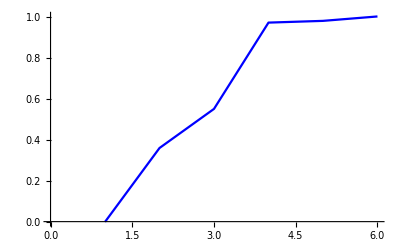

```mathematica
gb=ListLinePlot[sig,PlotStyle->Blue]
```

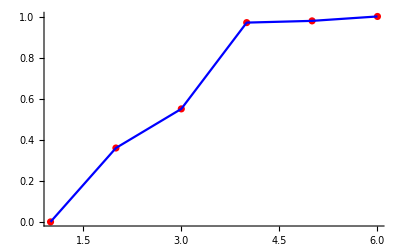

```mathematica
Show[{ga,gb},PlotRange->All]
```

```mathematica
Expand[((f[x]+67.66395412087394)*e)]
```

1.92719×10^-9-(2.43321×10^-7)/(1+(-3.5+x)^2)+2.84492×10^-8 x+(6.95204×10^-8 x)/(1+(-3.5+x)^2)-5.67645×10^-9 x^2-3.38632×10^-10 x^3+8.34551×10^-11 x^4+5.08476×10^-12 x^5

```mathematica
Clear[Qu,Qd]
```

```mathematica
Reduce[{(8*Pi/3)*Qu^3+2*(8*Pi/3)*Qd^3==mp,2*(8*Pi/3)*Qu^3+(8*Pi/3)*Qd^3==mn},{Qd,Qu}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(Qd==-2.02532×10^-9-3.50795×10^-9 ⅈ||Qd==4.05063×10^-9||Qd==-2.02532×10^-9+3.50795×10^-9 ⅈ)&&(Qu==-2.02806×10^-9+3.5127×10^-9 ⅈ||Qu==-2.02806×10^-9-3.5127×10^-9 ⅈ||Qu==4.05612×10^-9)

```mathematica
qq={Qd,Qu}/.Solve[{(8*Pi/3)*Qu^3+2*(8*Pi/3)*Qd^3==mp,2*(8*Pi/3)*Qu^3+(8*Pi/3)*Qd^3==mn},{Qd,Qu}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{-2.02532×10^-9-3.50795×10^-9 ⅈ,-2.02806×10^-9-3.5127×10^-9 ⅈ},{-2.02532×10^-9-3.50795×10^-9 ⅈ,-2.02806×10^-9+3.5127×10^-9 ⅈ},{-2.02532×10^-9-3.50795×10^-9 ⅈ,4.05612×10^-9},{-2.02532×10^-9+3.50795×10^-9 ⅈ,-2.02806×10^-9-3.5127×10^-9 ⅈ},{-2.02532×10^-9+3.50795×10^-9 ⅈ,-2.02806×10^-9+3.5127×10^-9 ⅈ},{-2.02532×10^-9+3.50795×10^-9 ⅈ,4.05612×10^-9},{4.05063×10^-9,-2.02806×10^-9-3.5127×10^-9 ⅈ},{4.05063×10^-9,-2.02806×10^-9+3.5127×10^-9 ⅈ},{4.05063×10^-9,4.05612×10^-9}}

```mathematica
Apply[Plus,qq]/9
```

{0.-4.59545×10^-26 ⅈ,0.+0. ⅈ}

```mathematica
Length[qq]
```

9

```mathematica
Abs[qq]/e
```

{{8.43319,8.44461},{8.43319,8.44461},{8.43319,8.44461},{8.43319,8.44461},{8.43319,8.44461},{8.43319,8.44461},{8.43319,8.44461},{8.43319,8.44461},{8.43319,8.44461}}

```mathematica
(*elliptic mass quarks*)
```

```mathematica
mq={(8*Pi/3)*Qd^3,(8*Pi/3)*Qu^3}/.Solve[{(8*Pi/3)*Qu^3+2*(8*Pi/3)*Qd^3==mp,2*(8*Pi/3)*Qu^3+(8*Pi/3)*Qd^3==mn},{Qd,Qu}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Apply[Plus,{{5.567852641493672*^-25-4.808495334478647*^-41 ⅈ,5.590512487012657*^-25+4.808495334478647*^-41 ⅈ},{5.567852641493672*^-25-4.808495334478647*^-41 ⅈ,5.590512487012657*^-25-4.808495334478647*^-41 ⅈ},{5.567852641493672*^-25-4.808495334478647*^-41 ⅈ,5.590512487012655*^-25},{5.567852641493672*^-25+4.808495334478647*^-41 ⅈ,5.590512487012657*^-25+4.808495334478647*^-41 ⅈ},{5.567852641493672*^-25+4.808495334478647*^-41 ⅈ,5.590512487012657*^-25-4.808495334478647*^-41 ⅈ},{5.567852641493672*^-25+4.808495334478647*^-41 ⅈ,5.590512487012655*^-25},{5.567852641493672*^-25,5.590512487012657*^-25+4.808495334478647*^-41 ⅈ},{5.567852641493672*^-25,5.590512487012657*^-25-4.808495334478647*^-41 ⅈ},{5.567852641493672*^-25,5.590512487012655*^-25}}]/9
```

{5.56785×10^-25-1.13287×10^-57 ⅈ,5.59051×10^-25+0. ⅈ}

```mathematica
mq/me
```

{{611.222-5.27862×10^-14 ⅈ,613.709+5.27862×10^-14 ⅈ},{611.222-5.27862×10^-14 ⅈ,613.709-5.27862×10^-14 ⅈ},{611.222-5.27862×10^-14 ⅈ,613.709},{611.222+5.27862×10^-14 ⅈ,613.709+5.27862×10^-14 ⅈ},{611.222+5.27862×10^-14 ⅈ,613.709-5.27862×10^-14 ⅈ},{611.222+5.27862×10^-14 ⅈ,613.709},{611.222,613.709+5.27862×10^-14 ⅈ},{611.222,613.709-5.27862×10^-14 ⅈ},{611.222,613.709}}

```mathematica
(me+mhiggs)/(2*mp)
```

```mathematica
(*seems to be a monopole mass and charge connected to up and down quarks: complex charge for monopole*)
```

```mathematica
Solve[4.808495334478647*^-41 ⅈ==(8*Pi/3)*Q0^3,Q0]
```

{{Q0→-1.55058×10^-14+8.95228×10^-15 ⅈ},{Q0→0.-1.79046×10^-14 ⅈ},{Q0→1.55058×10^-14+8.95228×10^-15 ⅈ}}

```mathematica
(* negative dimension connected to magnetic monopole*)
```

```mathematica
Solve[1.7904554992680818*^-14==e/α^s,s]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s→-2.07249}}